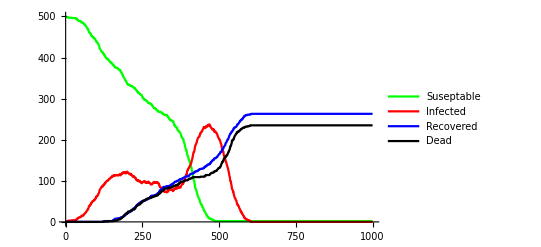

```mathematica
points=500;
gen=1000;
r=0.9;
xran=50;
(*x area range of the population in question*)
yran=50;(*y area range of the population in question*)
susceptable={};
n=25;
infected={};
recovered={};
dead={};
c=Table[0,{i,1,points}];
f=Table[0,{i,1,points}];
Table[{Subscript[vx, t]=RandomReal[{-0.5,0.5}],Subscript[vy, t]=RandomReal[{-0.5,0.5}]},{t,1,points}];
Table[{Subscript[col, t]=Green,Point[{Subscript[x, t]=RandomReal[RandomChoice[{{-xran,-xran/2},{xran/2,xran}}]],Subscript[y, t]=RandomReal[{-yran,yran}]}]},{t,1,points}]//MatrixForm;
Subscript[col, 21]=Red;(*initially 1 infectious person is introduced in the sus population*)
Do[
{
AppendTo[infected,{i,Count[Table[Subscript[col, m],{m,1,points}],Red]}],
AppendTo[susceptable,{i,Count[Table[Subscript[col, m],{m,1,points}],Green]}],
AppendTo[recovered,{i,Count[Table[Subscript[col, m],{m,1,points}],Blue]}],
AppendTo[dead,{i,Count[Table[Subscript[col, m],{m,1,points}],Black]}],
Subscript[lp, i]=ListPlot[{susceptable,infected,recovered,dead},PlotStyle->{Green,Red,Blue,Black},PlotLegends->{"Suseptable","Infected","Recovered","Dead"},PlotRange->{Automatic,{0,points}},Joined->True],
Do[{Subscript[x, t]=Subscript[x, t]+Subscript[vx, t],Subscript[y, t]=Subscript[y, t]+Subscript[vy, t],
If[(Subscript[x, t]>=-xran/2)&&(Subscript[x, t]<=xran/2),If[!(Subscript[y, t]≥-yran/n &&Subscript[y, t]≤yran/n),Subscript[vx, t]=-Subscript[vx, t]]],(*innner wall hitting condition and entering nozzle condition*)
If[(Subscript[x, t]>=-xran/2)&&(Subscript[x, t]<=xran/2)&&(Subscript[y, t]>=-yran/n)&&(Subscript[y, t]≤yran/n),f[[t]]=1,f[[t]]=0],(*flagging particle entering a nozzle*)
If[f[[t]]==1 && ((Subscript[y, t]+Subscript[vy, t]<=-yran/n)||(Subscript[y, t]+Subscript[vy, t]>=yran/n)),Subscript[vy, t]=-Subscript[vy, t]],(*nozzle wall hitting condition of flagged particles*)
If[Subscript[x, t]<=-xran||Subscript[x, t]≥xran,Subscript[vx, t]=-Subscript[vx, t]],(*right,left center two wall condition*)
If[Subscript[y, t]<=-yran||Subscript[y, t]≥yran,Subscript[vy, t]=-Subscript[vy, t]],(*upper and lower wall condition*)

If[Subscript[col, t]==Black,{Subscript[vx, t]=0,Subscript[vy, t]=0}],If[Subscript[col, t]==Red,{Do[If[(Subscript[x, i]-Subscript[x, t])^2+(Subscript[y, i]-Subscript[y, t])^2≤r^2 &&Subscript[col, i]==Green,Subscript[col, i]=Red],{i,1,points}],c[[t]]=c[[t]]+1,If[c[[t]]≥120,Subscript[col, t]=RandomChoice[{Blue,Black}]]}]},{t,1,points}],Subscript[p, i]=Graphics[Table[{Subscript[col, n],PointSize[0.025],Point[{Subscript[x, n],Subscript[y, n]}]},{n,1,points}],PlotRange->{{-xran,xran},{-yran,yran}}]},{i,1,gen}]
ListPlot[{susceptable,infected,recovered,dead},PlotStyle->{Green,Red,Blue,Black},PlotLegends->{"Suseptable","Infected","Recovered","Dead"},PlotRange->{Automatic,{0,points}},Joined->True]
```

```mathematica
gif1=Table[Subscript[p, i],{i,1,gen}];
gif2=Table[Subscript[lp, i],{i,1,gen}];
Export["E:\\SIR_sim.gif",gif1];
Export["E:\\SIR_model.gif",gif2];
SystemOpen["E:\\SIR_model.gif"];
SystemOpen["E:\\SIR_sim.gif"];
```